```mathematica
k = 2 + 0.1 *19;
f[x_] = Exp[ Sqrt[x]] + k * Exp[-k * x]
```

ⅇ^(√x)+3.9 ⅇ^(-3.9 x)

```mathematica
FindMinimum[f[x],x]
```

{2.54501,{x→0.61213}}

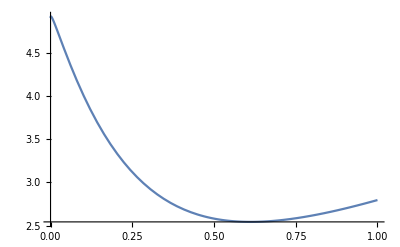

```mathematica
Plot [f[x],{x, 0,1}]
```

```mathematica
a = 0;
b = 2;
ϵ = 0.01;
"Scan"
min = 10;
minx = 3;
For[i=0, i< (b-a)/ϵ, i = i + ϵ, 
	If[f[i]<min, 
		min = f[i];
		minx = i]]
min  " - f[x]"
minx  " - x"
(b-a)/ϵ" - количество шагов"
```

Scan

2.54502  - f[x]

0.61  - x

```mathematica
200. " - количество шагов"
```

```mathematica
"Dichotomy"
a = 0;
b = 2;
ϵ = 0.01;
d  = 0;
While [ Abs[b-a]>ϵ, 
	c = (a + b)/2;
	d++
	If [f[c-ϵ]<f[c+ϵ], b = c, a = c]]
N[c = (a+b)/2 ]" - x"
f[c] " - f[x]"
d  " - количество шагов"
```

Dichotomy

0.613281  - x

2.54501  - f[x]

```mathematica
8 " - количество шагов"
```

```mathematica
"Fibonaccii"
n = 30;
counter = 0;
ϵ=0.01;
l=0;
r=2; 
lam = l + (r - l)*Fibonacci[n-2]/Fibonacci[n];
mu= l + (r - l)*Fibonacci[n-1]/Fibonacci[n];
For [k = 1, k < n-2, k++, 
		counter ++;
	If [f[lam]> f[mu], 
		l = lam;
		lam = mu;
		mu = l + Fibonacci[n-k-1]/Fibonacci[n-k] * (r - l),
			r = mu;
			mu = lam;
			lam = l + Fibonacci[n-k-2]/Fibonacci[n-k] * (r-l)]];
mu = lam + ϵ;
If [f[lam] = f[mu], l = lam,
	If [f[lam]<f[mu], r = mu]];
counter " - количество шагов"
f[(l+r)/2] " - f(x)"
N[(l+r)/2] " - x"
```

Fibonaccii

27  - количество шагов

2.54526  - f(x)

0.612134  - x